## latex

```mathematica
myData="/Users/dantopa/Mathematica_files/io/ert/freecad/data/";
```

### data

```mathematica
objs={"B20-standard-1m.obj","B20-standard-0.1m.obj","B20-standard-0.05m.obj","B20-standard-0.01m.obj","B20-standard-0.001m.obj","B20-mephisto-1-m.obj","B20-netgen-very-fine.obj"};
```

### method

```mathematica
$tick;
numFaces={};
allAreas={};
maxes={};
mins={};
Do[
(* point to file *)
file=objs[[k]];
target=myData<>file;
(* collect polygons *)
pgons=Import[target,"PolygonObjects"]/.Polygon[a_]:>Polygon/@a;
(* compute triangle areas *)
areas=Area/@pgons;
λ=Length[areas];
numFaces=AppendTo[numFaces,λ];
sareas=Sort[areas];
allAreas=AppendTo[allAreas,{Range[λ],sareas}ᵀ];
(* characterize *)
mx=Max[areas];
mn=Min[areas];
spectralRadius=Log[10,mx]-Log[10,mn];
maxes=AppendTo[maxes,{λ,mx}];
mins=AppendTo[mins,{λ,mn}];
(* describe *)
Print[lf,"file = ",file];
Print["number of triangles = ",λ];
Print["Maximum area    = ",mx];
Print["Minimum area    = ",mn];
Print["Spectral radius = ",spectralRadius];
(* list plot *)
gg=ListLogLogPlot[sareas,
ipad,
Frame->True,
PlotRange->Full,
PlotStyle->{{Blue},{Opacity[0.1]}},
PlotLabel->"Areas of "<>ToString[λ]<>" faces",
FrameLabel->{"Index","Face area, m^2"}];
(* glamor shot *)
ggg=Import[target,ImageSize->6 72];
(* export graphics *)
base=StringDrop[file,-4];
base=StringReplace[base,"."->"-"];
tresExport["dots-"<>base,gg];tresExport["views-"<>base,ggg];
,{k,1}];
tiempo[lf<>"analysis and graphics"];
```

file = B20-standard-1m.obj

number of triangles = 626

Maximum area    = 6.56699×10^7

Minimum area    = 352.762

Spectral radius = 5.26988

analysis and graphics
CPU time: 2.77329 sec
elapsed time: 5.288886 sec

```mathematica
gg
```

```mathematica
Show[{gg,Graphics[{Red,Line[{{-1,Log[352]},{630,Log[352]}}]}]}]
```

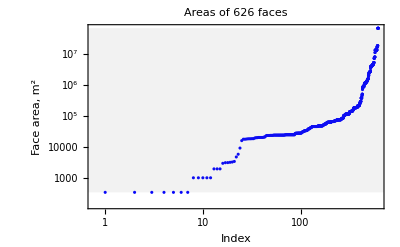

```mathematica
g1=Show[{gg,Graphics[{Gray,Opacity[0.1],Rectangle[{-1,Log[352]},{630,Log[6.6 10^7]}]}]}]
```

```mathematica
Rectangle[{-1,Log[352]},{630,Log[6.6 10^7]}]
```

Rectangle[{-1,Log[352]},{630,18.0052}]

```mathematica
tresExport["spectral-radius",g1]
```